```mathematica
directory=NotebookDirectory[];

b=8.6*10^(-11);
l=-21/58*b;
le=l/3;
lµ=l/3;
ltau=l/3;
(*ELETTRONI, MUONI e TAUONI*)
mmu=105.6583755;
gmu=2;
mtau=1.7768*10^3;
gtau=2;
ge=2;
gnu=1;
mnu=0;
me=0.511;


(*MESONI*)
mp=139.57018;
gp=1;
mkp=493.677;
gkp=1;
mk0=497.614;
gk0=1; (*devo considerare pero kL e Ks e le loro antiparticelle che sono loro stesse*)
mrho=776;
grho=1;(*devo considerare però i 3 rho differenti, rho 0, rho+ e rho-*)
momega=782.65;
gomega=1;
mlambda=1115.683;
glambda=2;
mlambdacharmed=2286.46;
glambdacharmed=2;
mlambdabottom=5620.2;
glambdabottom=2;


(*QUARK*)
mqu=2.3;
mqd=4.8;
mqch=1275;
mqs=95;
mqt=173210;
mqb=4180;
gq=3*2;
ggluon=16;

(*BOSONI DI GAUGE E HIGGS*)
mw=80.39*10^3;
gw=3; 
mz=91.19*10^3;
gz=3;
mh=124.97*10^3;
gh=1;

dnf[m_,u_,g_,T_,e_]:=g/(2*Pi^2)*(e^2-m^2)^(1/2)*e/(Exp[(e-u)/T]+1);
dnb[m_,u_,g_,T_,e_]:=g/(2*Pi^2)*(e^2-m^2)^(1/2)*e/(Exp[(e-u)/T]-1);
def[m_,u_,g_,T_,e_]:= g/(2*Pi^2)*(e^2-m^2)^(1/2)/(Exp[(e-u)/T]+1)*e^2;
deb[m_,u_,g_,T_,e_]:= g/(2*Pi^2)*(e^2-m^2)^(1/2)/(Exp[(e-u)/T]-1)*e^2;
dpf[m_,u_,g_,T_,e_]:= g/(6*Pi^2)*(e^2-m^2)^(3/2)/(Exp[(e-u)/T]+1);
dpb[m_,u_,g_,T_,e_]:= g/(6*Pi^2)*(e^2-m^2)^(3/2)/(Exp[(e-u)/T]-1);

(*THERMODYNAMICS*)

(*NUMBER DENSITY*)
nf[m_,u_,g_,T_]:=NIntegrate[g/(2*Pi^2)*e*(e^2-m^2)^(1/2)/(Exp[(e-u)/T]+1),{e,m,+Infinity}];
nb[m_,u_,g_,T_]:=NIntegrate[g/(2*Pi^2)*e*(e^2-m^2)^(1/2)/(Exp[(e-u)/T]-1),{e,m,+Infinity}];
nfpap[m_,u_,g_,T_]:=NIntegrate[g/(2*Pi^2)*e*(e^2-m^2)^(1/2)/(Exp[(e-u)/T]+1),{e,m,+Infinity}]+NIntegrate[g/(2*Pi^2)*e*(e^2-m^2)^(1/2)/(Exp[(e+u)/T]+1),{e,m,+Infinity}];
nbpap[m_,u_,g_,T_]:=NIntegrate[g/(2*Pi^2)*e*(e^2-m^2)^(1/2)/(Exp[(e-u)/T]-1),{e,m,+Infinity}]+NIntegrate[g/(2*Pi^2)*e*(e^2-m^2)^(1/2)/(Exp[(e+u)/T]-1),{e,m,+Infinity}];


 (*NET NUMBER DENSITY*)
nasymf[m_,u_,g_,T_]:=NIntegrate[g/(2*Pi^2)*e*(e^2-m^2)^(1/2)*(1/(Exp[(e-u)/T]+1)-1/(Exp[(e+u)/T]+1)),{e,m,+Infinity}];
nasymb[m_,u_,g_,T_]:=NIntegrate[g/(2*Pi^2)*e*(e^2-m^2)^(1/2)*(1/(Exp[(e-u)/T]-1)-1/(Exp[(e+u)/T]-1)),{e,m,+Infinity}];

(*LA MIA RISCRITTURA*)

nasymfDF[m_,u_,g_,T_]:=If[m>0,g/(Pi^2)*Sinh[u/T]*Exp[-m/T]*(T*m)^(3/2)*NIntegrate[(Exp[x]*(1+T*x/m)*Sqrt[(2+T/m*x)*x])/((Exp[x-u/T]+Exp[-m/T])*(Exp[x+u/T]+Exp[-m/T])),{x,0,+Infinity}],(g T^3 PolyLog[3,-ⅇ^(-u/T)])/π^2-(g T^3 PolyLog[3,-ⅇ^(u/T)])/π^2]


(*Riscrittura Schwarz Stuke*)
nasymfSS[m_,u_,g_,T_]:=g/(2*Pi)*Sinh[u/T]*Exp[-m/T]*(T*m)^(3/2)*NIntegrate[(1+T*x/m)*Sqrt[(1+T/m*x)*x]/((Exp[x-u/T]+Exp[-m/T])*(Exp[x+u/T]+Exp[-m/T])),{x,0,+Infinity}]

(*ENERGY DENSITY*) 
ef[m_,u_,g_,T_]:= NIntegrate[g/(2*Pi^2)*(e^2-m^2)^(1/2)/(Exp[(e-u)/T]+1)*e^2,{e,m,+Infinity}]; 
eb[m_,u_,g_,T_]:= NIntegrate[g/(2*Pi^2)*(e^2-m^2)^(1/2)/(Exp[(e-u)/T]-1)*e^2,{e,m,+Infinity}];

efpap[m_,u_,g_,T_]:= NIntegrate[g/(2*Pi^2)*(e^2-m^2)^(1/2)*e^2/(Exp[(e-u)/T]+1),{e,m,+Infinity}]+NIntegrate[g/(2*Pi^2)*(e^2-m^2)^(1/2)*e^2/(Exp[(e+u)/T]+1),{e,m,+Infinity}];
ebpap[m_,u_,g_,T_]:= NIntegrate[g/(2*Pi^2)*(e^2-m^2)^(1/2)/(Exp[(e-u)/T]-1)*e^2,{e,m,+Infinity}]+NIntegrate[g/(2*Pi^2)*(e^2-m^2)^(1/2)/(Exp[(e+u)/T]-1)*e^2,{e,m,+Infinity}];

(*MY RESCRIPTION OF EFPAP*)
efpapDF[m_,u_,g_,T_]:=If[m>0,g/Pi^2*Exp[-m/T]*Sqrt[T^3*m^5]*NIntegrate[(1+T*x/m)^2*Sqrt[x*(T*x/m+2)]*(Exp[-m/T]+Exp[x]*Cosh[u/T])/((Exp[x-u/T]+Exp[-m/T])*(Exp[x+u/T]+Exp[-m/T])),{x,0,+Infinity}],-(3 g T^4 PolyLog[4,-ⅇ^(-u/T)])/π^2-(3 g T^4 PolyLog[4,-ⅇ^(u/T)])/π^2]

(*PRESSURE*)

pf[m_,u_,g_,T_]:= NIntegrate[g/(6*Pi^2)*(e^2-m^2)^(3/2)/(Exp[(e-u)/T]+1),{e,m,+Infinity}];
pb[m_,u_,g_,T_]:=  NIntegrate[g/(6*Pi^2)*(e^2-m^2)^(3/2)/(Exp[(e-u)/T]-1),{e,m,+Infinity}];

pfpap[m_,u_,g_,T_]:=  NIntegrate[g/(6*Pi^2)*(e^2-m^2)^(3/2)/(Exp[(e-u)/T]+1),{e,m,+Infinity}]+ NIntegrate[g/(6*Pi^2)*(e^2-m^2)^(3/2)/(Exp[(e+u)/T]+1),{e,m,+Infinity}];
pbpap[m_,u_,g_,T_]:=  NIntegrate[g/(6*Pi^2)*(e^2-m^2)^(3/2)/(Exp[(e-u)/T]-1),{e,m,+Infinity}]+ NIntegrate[g/(6*Pi^2)*(e^2-m^2)^(3/2)/(Exp[(e+u)/T]-1),{e,m,+Infinity}];
(*MY RESCRIPTON OF PFPAP*)
pfpapDF[m_,u_,g_,T_]:=If[m>0,g/(3*Pi^2)Exp[-m/T]Sqrt[T^5*m^3]*NIntegrate[(x*(T*x/m+2))^(3/2)*(Exp[-m/T]+Exp[x]*Cosh[u/T])/((Exp[x-u/T]+Exp[-m/T])*(Exp[x+u/T]+Exp[-m/T])),{x,0,+Infinity}],-(g T^4 PolyLog[4,-ⅇ^(-u/T)])/π^2-(g T^4 PolyLog[4,-ⅇ^(u/T)])/π^2]

(*ENTROPY*)
sf[m_,u_,g_,T_]:=1/T*(NIntegrate[g/(6*Pi^2)*(e^2-m^2)^(3/2)/(Exp[(e-u)/T]+1),{e,m,+Infinity}]+NIntegrate[g/(2*Pi^2)*(e^2-m^2)^(1/2)*e^2/(Exp[(e-u)/T]+1),{e,m,+Infinity}]-u*nf[m,u,g,T] );
sb[m_,u_,g_,T_]:=1/T*( NIntegrate[g/(6*Pi^2)*(e^2-m^2)^(3/2)/(Exp[(e-u)/T]-1),{e,m,+Infinity}]+NIntegrate[g/(2*Pi^2)*(e^2-m^2)^(1/2)*e^2/(Exp[(e-u)/T]-1),{e,m,+Infinity}]-u*nb[m,u,g,T] );

(*ENTROPY WITH THE CONTRIBUTION BOTH OF THE PARTICLE AND ANTIPARTICLE*)
sfpap[m_,u_,g_,T_]:=1/T*(efpap[m,u,g,T]+pfpap[m,u,g,T] -u*nasymf[m,u,g,T]);
sbpap[m_,u_,g_,T_]:=1/T*( ebpap[m,u,g,T]+pbpap[m,u,g,T] -u*nasymb[m,u,g,T]);

(*MY RESCRITPION OF SFPAP*)
sfpapDF[m_,u_,g_,T_]:=1/T*(pfpapDF[m,u,g,T] +efpapDF[m,u,g,T]-u*nasymfDF[m,u,g,T]);


(*TOTAL ENTROPY*)
stotDF[uu_,ue_,unuµ_,unue_,unutau_,T_]:=(*QUARK UP DOWN STRANGE CHARM BOTTOM TOP*)sfpapDF[mqu,uu,gq,T]+sfpapDF[mqd,uu+ue-unue,gq,T]+sfpapDF[mqs,uu+ue-unue,gq,T]+sfpapDF[mqch,uu,gq,T]+sfpapDF[mqb,uu+ue-unue,gq,T]+sfpapDF[mqt,uu,gq,T](*ELETTRONE E MUONE*)+sfpapDF[me,ue,ge,T]+sfpapDF[mmu,ue-unue+unuµ,ge,T]+(*NEUTRINI*)sfpapDF[mnu,unue,gnu,T]+sfpapDF[mnu,unuµ,gnu,T]+sfpapDF[mnu,unutau,gnu,T](*BOSONI*)+sb[0,0,2,T]+sb[0,0,ggluon,T];
```

```mathematica
(*Calculation of the starting points*)


TxDF=.;
µexDF=.;
µuxDF=.;
µnuexDF=.;
µnuµxDF=.;
µnutauxDF=.;
µeDF=.;
µuDF=.;
µnueDF=.;
µnuµDF=.;
µnutauDF=.;




TxDF={};
µexDF={};
µuxDF={};
µnuexDF={};
µnuµxDF={};
µnutauxDF={};


µestartDF=.;
µustartDF=.;
µnuµstartDF=.;
µnuestartDF=.;
µnutaustartDF=.;

µestartDF=10^-9;
µustartDF=10^-9;
µnuµstartDF=10^-9;
µnuestartDF=10^-9;
µnutaustartDF=10^-9;

i=.;
i=1;
T=10^-6
While[T<100,i++;
Sol=FindRoot[{0==nasymfDF[me,µe,ge,T]+nasymfDF[mnu,µnue,gnu,T]-le*stotDF[µu,µe,µnuµ,µnue,µnutau,T],0==nasymfDF[mmu,µe-µnue+µnuµ,ge,T]+nasymfDF[mnu,µnuµ,gnu,T]-lµ*stotDF[µu,µe,µnuµ,µnue,µnutau,T],0==nasymfDF[mtau,µe-µnue+µnutau,ge,T]+nasymfDF[mnu,µnutau,gnu,T]-ltau*stotDF[µu,µe,µnuµ,µnue,µnutau,T],3*b*stotDF[µu,µe,µnuµ,µnue,µnutau,T]==nasymfDF[mqu,µu,gq,T]+nasymfDF[mqd,µu+µe-µnue,gq,T]+nasymfDF[mqch,µu,gq,T]+nasymfDF[mqs,µu+µe-µnue,gq,T]+nasymfDF[mqb,µu+µe-µnue,gq,T],0==-nasymfDF[me,µe,ge,T]-nasymfDF[mmu,µe-µnue+µnuµ,ge,T]-nasymfDF[mtau,µe-µnue+µnutau,ge,T]+ 2/3*nasymfDF[mqu,µu,gq,T]-1/3*nasymfDF[mqd,µu+µe-µnue,gq,T]+2/3*nasymfDF[mqch,µu,gq,T]-1/3*nasymfDF[mqs,µu+µe-µnue,gq,T]-1/3*nasymfDF[mqb,µu+µe-µnue,gq,T]+2/3*nasymfDF[mqt,µu,gq,T]},{{µe,µestartDF},{µu,µustartDF},{µnuµ,µnuµstartDF},{µnue,µnuestartDF},{µnutau,µnutaustartDF}}];
AppendTo[µexDF,µe/.  Sol];
AppendTo[µuxDF,µu/.  Sol];
AppendTo[µnuexDF,µnue/.  Sol];
AppendTo[µnuµxDF,µnuµ/.  Sol];
AppendTo[µnutauxDF,µnutau/.  Sol];
µestartDF=Last[µexDF];
µustartDF=Last[µuxDF];
µnuµstartDF=Last[µnuµxDF];
µnuestartDF=Last[µnuexDF];
µnutaustartDF=Last[µnutauxDF];
Print[T//N];
Sol=.;
T'=T;
T=T'*i;
]
µestartDF
µustartDF
µnuestartDF
µnuµstartDF
µnutaustartDF
```

1/1000000

General::munfl: Exp[-511000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::inumr: The integrand (ⅇ^x (1+1.95695×10^-6 x) √((2+1.95695×10^-6 x) x))/((0.+ⅇ^(x-1000000 µe)) (0.+ⅇ^(x+1000000 µe))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::inumr: The integrand (((2+4.34783×10^-7 x) x)^(3/2) (0.+ⅇ^x Cosh[1000000 µu]))/((0.+ⅇ^(x-1000000 µu)) (0.+ⅇ^(x+1000000 µu))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {µe,µu,µnuµ,µnue,µnutau} = {1.×10^-9,1.×10^-9,1.×10^-9,1.×10^-9,1.×10^-9}. Try perturbing the initial point(s).

1.×10^-6

FindRoot::jsing: Encountered a singular Jacobian at the point {µe,µu,µnuµ,µnue,µnutau} = {1.×10^-9,1.×10^-9,1.×10^-9,1.×10^-9,1.×10^-9}. Try perturbing the initial point(s).

2.×10^-6

$Aborted

1.×10^-9

1.×10^-9

1.×10^-9

«2 more identical outputs»

```mathematica
(*Calculation of the starting points*)


TxDF=.;
µexDF=.;
µuxDF=.;
µnuexDF=.;
µnuµxDF=.;
µnutauxDF=.;
µeDF=.;
µuDF=.;
µnueDF=.;
µnuµDF=.;
µnutauDF=.;




TxDF={};
µexDF={};
µuxDF={};
µnuexDF={};
µnuµxDF={};
µnutauxDF={};


µestartDF=.;
µustartDF=.;
µnuµstartDF=.;
µnuestartDF=.;
µnutaustartDF=.;

µestartDF=10^-9;
µustartDF=10^-9;
µnuµstartDF=10^-9;
µnuestartDF=10^-9;
µnutaustartDF=10^-9;

i=.;
i=1;
T=10^-6
While[T<100,i++;
Sol=FindRoot[{0==nasymfDF[me,µe,ge,T]+nasymfDF[mnu,µnue,gnu,T]-le*stotDF[µu,µe,µnuµ,µnue,µnutau,T],0==nasymfDF[mmu,µe-µnue+µnuµ,ge,T]+nasymfDF[mnu,µnuµ,gnu,T]-lµ*stotDF[µu,µe,µnuµ,µnue,µnutau,T],0==nasymfDF[mtau,µe-µnue+µnutau,ge,T]+nasymfDF[mnu,µnutau,gnu,T]-ltau*stotDF[µu,µe,µnuµ,µnue,µnutau,T],3*b*stotDF[µu,µe,µnuµ,µnue,µnutau,T]==nasymfDF[mqu,µu,gq,T]+nasymfDF[mqd,µu+µe-µnue,gq,T]+nasymfDF[mqch,µu,gq,T]+nasymfDF[mqs,µu+µe-µnue,gq,T]+nasymfDF[mqb,µu+µe-µnue,gq,T],0==-nasymfDF[me,µe,ge,T]-nasymfDF[mmu,µe-µnue+µnuµ,ge,T]-nasymfDF[mtau,µe-µnue+µnutau,ge,T]+ 2/3*nasymfDF[mqu,µu,gq,T]-1/3*nasymfDF[mqd,µu+µe-µnue,gq,T]+2/3*nasymfDF[mqch,µu,gq,T]-1/3*nasymfDF[mqs,µu+µe-µnue,gq,T]-1/3*nasymfDF[mqb,µu+µe-µnue,gq,T]+2/3*nasymfDF[mqt,µu,gq,T]},{{µe,µestartDF},{µu,µustartDF},{µnuµ,µnuµstartDF},{µnue,µnuestartDF},{µnutau,µnutaustartDF}}];
AppendTo[µexDF,µe/.  Sol];
AppendTo[µuxDF,µu/.  Sol];
AppendTo[µnuexDF,µnue/.  Sol];
AppendTo[µnuµxDF,µnuµ/.  Sol];
AppendTo[µnutauxDF,µnutau/.  Sol];
µestartDF=Last[µexDF];
µustartDF=Last[µuxDF];
µnuµstartDF=Last[µnuµxDF];
µnuestartDF=Last[µnuexDF];
µnutaustartDF=Last[µnutauxDF];
Print[T//N];
Sol=.;
T'=T;
T=T'*i;
]
µestartDF
µustartDF
µnuestartDF
µnuµstartDF
µnutaustartDF





(*µ CALCULATION*)
µestartDF
TxDF=.;
µexDF=.;
µuxDF=.;
µnuexDF=.;
µnuµxDF=.;
µnutauxDF=.;
µeDF=.;
µuDF=.;
µnueDF=.;
µnuµDF=.;
µnutauDF=.;




TxDF={};
µexDF={};
µuxDF={};
µnuexDF={};
µnuµxDF={};
µnutauxDF={};




For[i=0,i<=40,i++,T=i*10+100;
AppendTo[TxDF,T];
Sol=FindRoot[{0==nasymfDF[me,µe,ge,T]+nasymfDF[mnu,µnue,gnu,T]-le*stotDF[µu,µe,µnuµ,µnue,µnutau,T],0==nasymfDF[mmu,µe-µnue+µnuµ,ge,T]+nasymfDF[mnu,µnuµ,gnu,T]-lµ*stotDF[µu,µe,µnuµ,µnue,µnutau,T],0==nasymfDF[mtau,µe-µnue+µnutau,ge,T]+nasymfDF[mnu,µnutau,gnu,T]-ltau*stotDF[µu,µe,µnuµ,µnue,µnutau,T],3*b*stotDF[µu,µe,µnuµ,µnue,µnutau,T]==nasymfDF[mqu,µu,gq,T]+nasymfDF[mqd,µu+µe-µnue,gq,T]+nasymfDF[mqch,µu,gq,T]+nasymfDF[mqs,µu+µe-µnue,gq,T]+nasymfDF[mqb,µu+µe-µnue,gq,T],0==-nasymfDF[me,µe,ge,T]-nasymfDF[mmu,µe-µnue+µnuµ,ge,T]-nasymfDF[mtau,µe-µnue+µnutau,ge,T]+ 2/3*nasymfDF[mqu,µu,gq,T]-1/3*nasymfDF[mqd,µu+µe-µnue,gq,T]+2/3*nasymfDF[mqch,µu,gq,T]-1/3*nasymfDF[mqs,µu+µe-µnue,gq,T]-1/3*nasymfDF[mqb,µu+µe-µnue,gq,T]+2/3*nasymfDF[mqt,µu,gq,T]},{{µe,µestartDF},{µu,µustartDF},{µnuµ,µnuµstartDF},{µnue,µnuestartDF},{µnutau,µnutaustartDF}}];
AppendTo[µexDF,µe/.  Sol];
AppendTo[µuxDF,µu/.  Sol];
AppendTo[µnuexDF,µnue/.  Sol];
AppendTo[µnuµxDF,µnuµ/.  Sol];
AppendTo[µnutauxDF,µnutau/.  Sol];
µestartDF=Last[µexDF];
µustartDF=Last[µuxDF];
µnuµstartDF=Last[µnuµxDF];
µnuestartDF=Last[µnuexDF];
µnutaustartDF=Last[µnutauxDF];
Print[i];
Sol=.;
]
```

1/1000000

General::munfl: Exp[-511000.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::inumr: The integrand (ⅇ^x (1+1.95695×10^-6 x) √((2+1.95695×10^-6 x) x))/((0.+ⅇ^(x-1000000 µe)) (0.+ⅇ^(x+1000000 µe))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

NIntegrate::inumr: The integrand (((2+4.34783×10^-7 x) x)^(3/2) (0.+ⅇ^x Cosh[1000000 µu]))/((0.+ⅇ^(x-1000000 µu)) (0.+ⅇ^(x+1000000 µu))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

FindRoot::jsing: Encountered a singular Jacobian at the point {µe,µu,µnuµ,µnue,µnutau} = {1.×10^-9,1.×10^-9,1.×10^-9,1.×10^-9,1.×10^-9}. Try perturbing the initial point(s).

1.×10^-6

FindRoot::jsing: Encountered a singular Jacobian at the point {µe,µu,µnuµ,µnue,µnutau} = {1.×10^-9,1.×10^-9,1.×10^-9,1.×10^-9,1.×10^-9}. Try perturbing the initial point(s).

2.×10^-6

FindRoot::jsing: Encountered a singular Jacobian at the point {µe,µu,µnuµ,µnue,µnutau} = {1.×10^-9,1.×10^-9,1.×10^-9,1.×10^-9,1.×10^-9}. Try perturbing the initial point(s).

General::stop: Further output of FindRoot::jsing will be suppressed during this calculation.

6.×10^-6

0.000024

0.00012

0.00072

0.00504

0.04032

0.36288

3.6288

39.9168

-7.75968×10^-9

7.93507×10^-8

-4.50453×10^-8

-5.01287×10^-8

-6.05643×10^-8

-7.75968×10^-9

NIntegrate::inumr: The integrand (ⅇ^x (1+195.695 x) √(x (2+195.695 x)))/((0.994903+ⅇ^(x-µe/100)) (0.994903+ⅇ^(x+µe/100))) has evaluated to non-numerical values for all sampling points in the region with boundaries {{∞,0.}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

General::munfl: Exp[-1732.1] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

0

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

1

2

3

4

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in e near {e} = {1226.83}. NIntegrate obtained 1.11033×10^8 and 225.251 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in e near {e} = {1226.83}. NIntegrate obtained 3.33099×10^8 and 675.753 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in e near {e} = {1226.83}. NIntegrate obtained 8.88264×10^8 and 1802.01 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

5

6

7

8

9

10

11

12

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

13

14

15

16

17

18

19

20

21

22

23

24

25

26

27

28

29

30

31

32

33

34

35

36

37

38

39

40

```mathematica
(*CRE UN FILE DI TESTO IN CON T E I VARI POTENZIALI CHIMICI*)
µB=µuxDF+2*(µuxDF+µexDF-µnuexDF);
µq=µexDF-µnuexDF;
Dati={TxDF,µB,µq,µuxDF,µexDF,µnuµxDF,µnuexDF,µnutauxDF};
directory=NotebookDirectory[];
percorsoCompleto=FileNameJoin[{directory,"T_µ.txt"}];

Export[percorsoCompleto,Transpose[Dati],"Table","FieldSeparators"->"\t"];
```

General::munfl: Exp[-1732.1] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1574.64] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-1443.42] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in e near {e} = {1226.83}. NIntegrate obtained 1.11033×10^8 and 225.251 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in e near {e} = {1226.83}. NIntegrate obtained 3.33099×10^8 and 675.753 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in e near {e} = {3577.83}. NIntegrate obtained 5.34724×10^6 and 6.71317 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

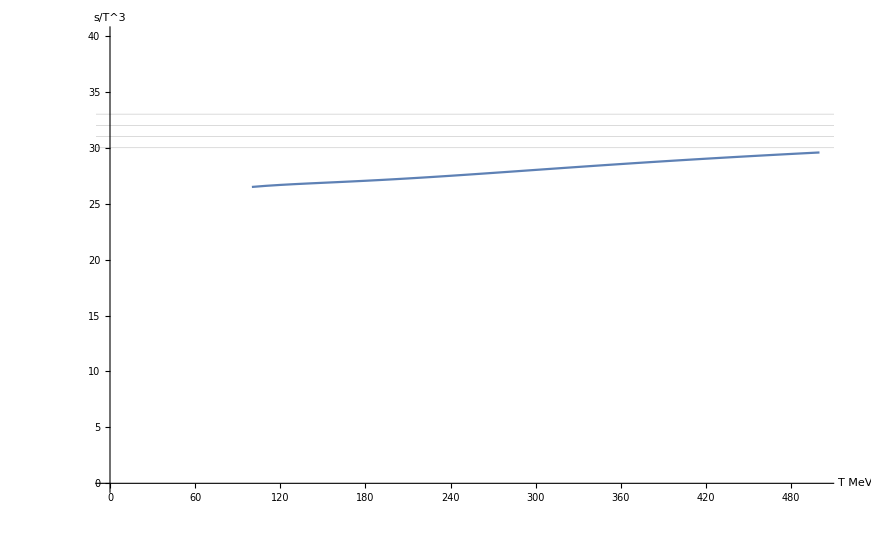

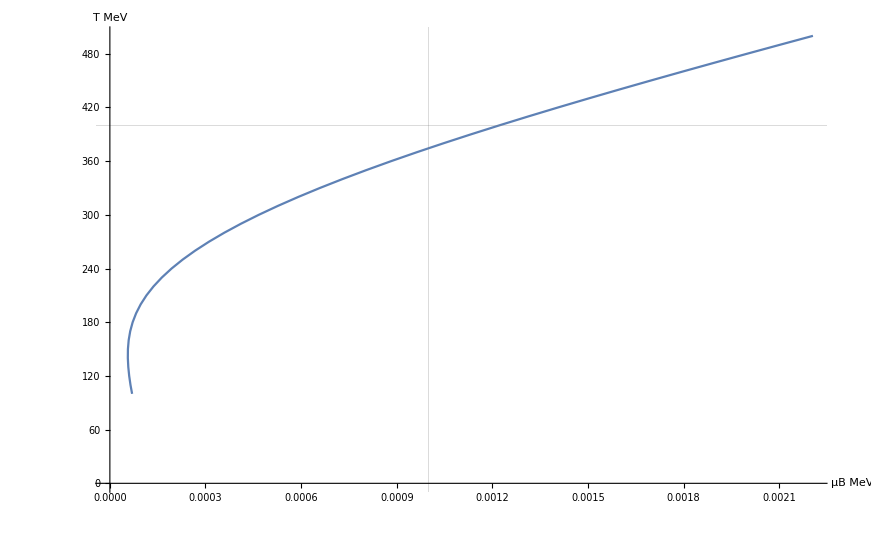

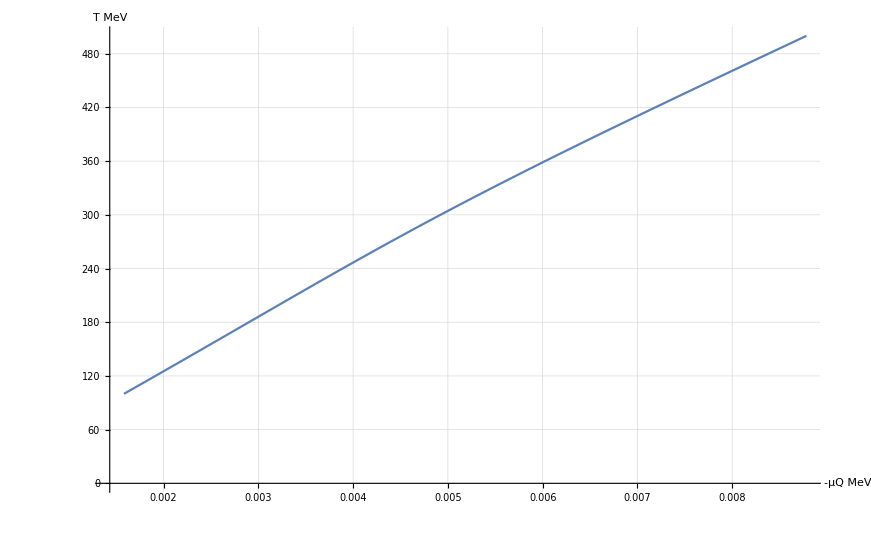

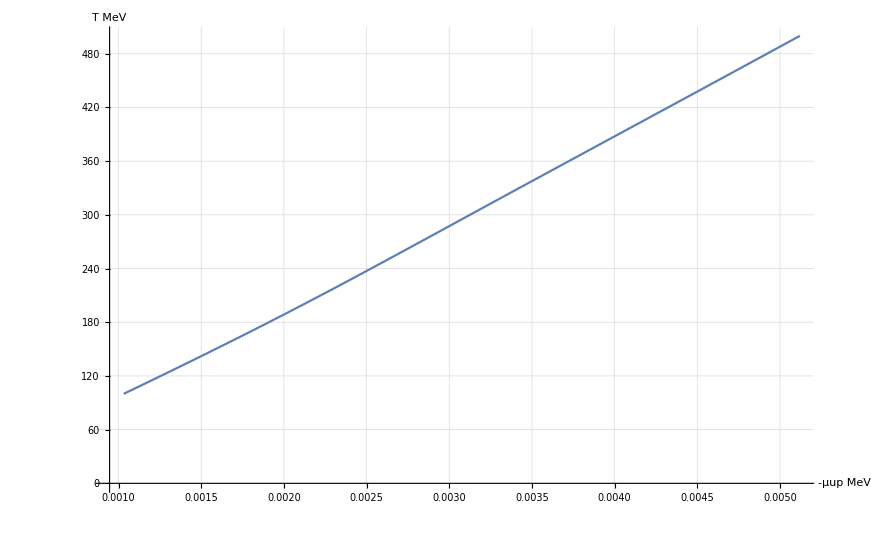

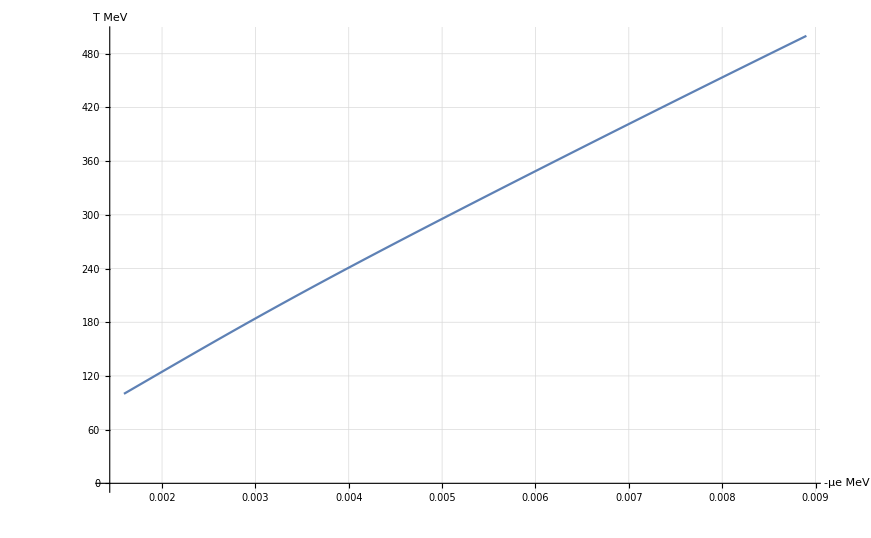

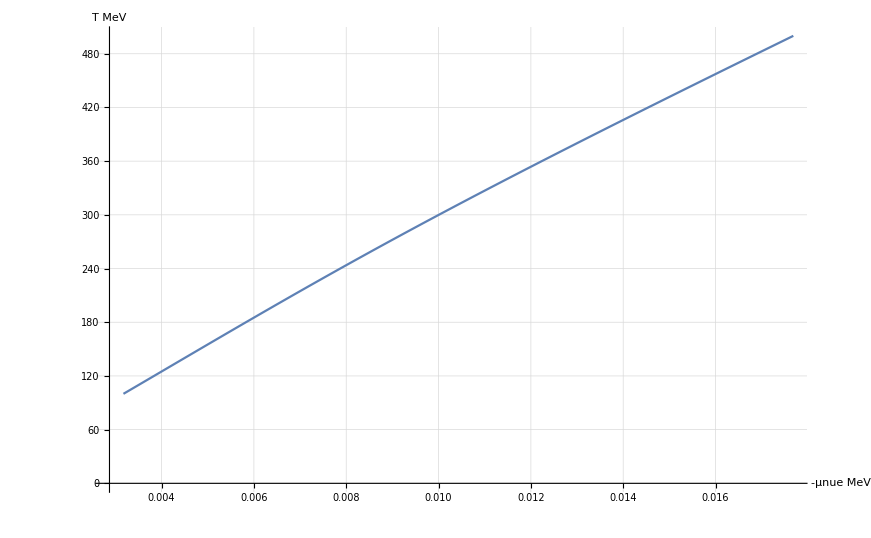

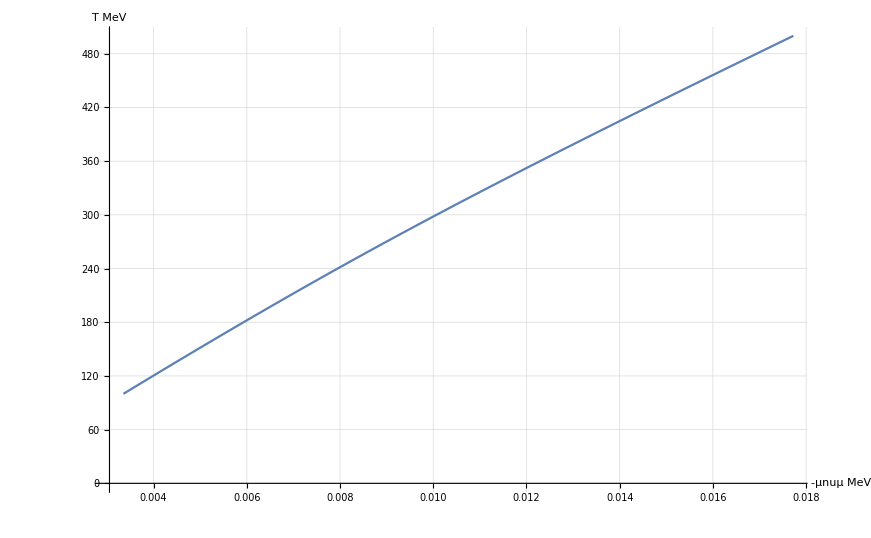

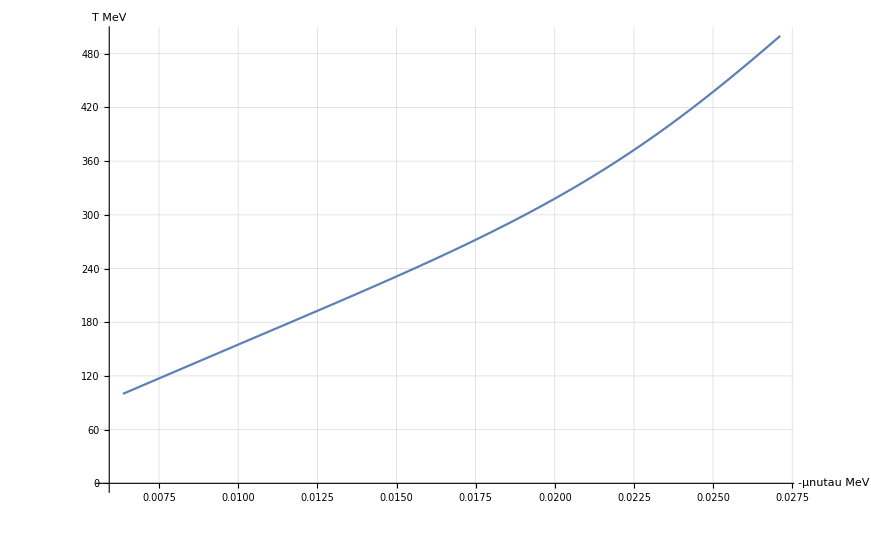

```mathematica
(*PLOT TRAIETTORIE DEI POT. CHIMICI*)
µB=µuxDF+2*(µuxDF+µexDF-µnuexDF);
µq=µexDF-µnuexDF;


ListLinePlot[Transpose[{TxDF,stotDF[µuxDF,µexDF,µnuµxDF,µnuexDF,µnutauxDF,TxDF]/TxDF^3}],AxesLabel->{"T MeV","s/T^3"},GridLines->Automatic,PlotRange->{{0,500},{0,40}}]
ListLinePlot[Transpose[{µB,TxDF}],AxesLabel->{"µB MeV","T MeV"},GridLines->{{0.001,30,31,32,33},{400}}]
ListLinePlot[Transpose[{µq,TxDF}],AxesLabel->{"-µQ MeV","T MeV"},GridLines->Automatic]
ListLinePlot[Transpose[{-µuxDF,TxDF}],AxesLabel->{"-µup MeV","T MeV"},GridLines->Automatic]
ListLinePlot[Transpose[{-µexDF,TxDF}],AxesLabel->{"-µe MeV","T MeV"},GridLines->Automatic]
ListLinePlot[Transpose[{-µnuexDF,TxDF}],AxesLabel->{"-µnue MeV","T MeV"},GridLines->Automatic]
ListLinePlot[Transpose[{-µnuµxDF,TxDF}],AxesLabel->{"-µnuµ MeV","T MeV"},GridLines->Automatic]
ListLinePlot[Transpose[{-µnutauxDF,TxDF}],AxesLabel->{"-µnutau MeV","T MeV"},GridLines->Automatic]
```

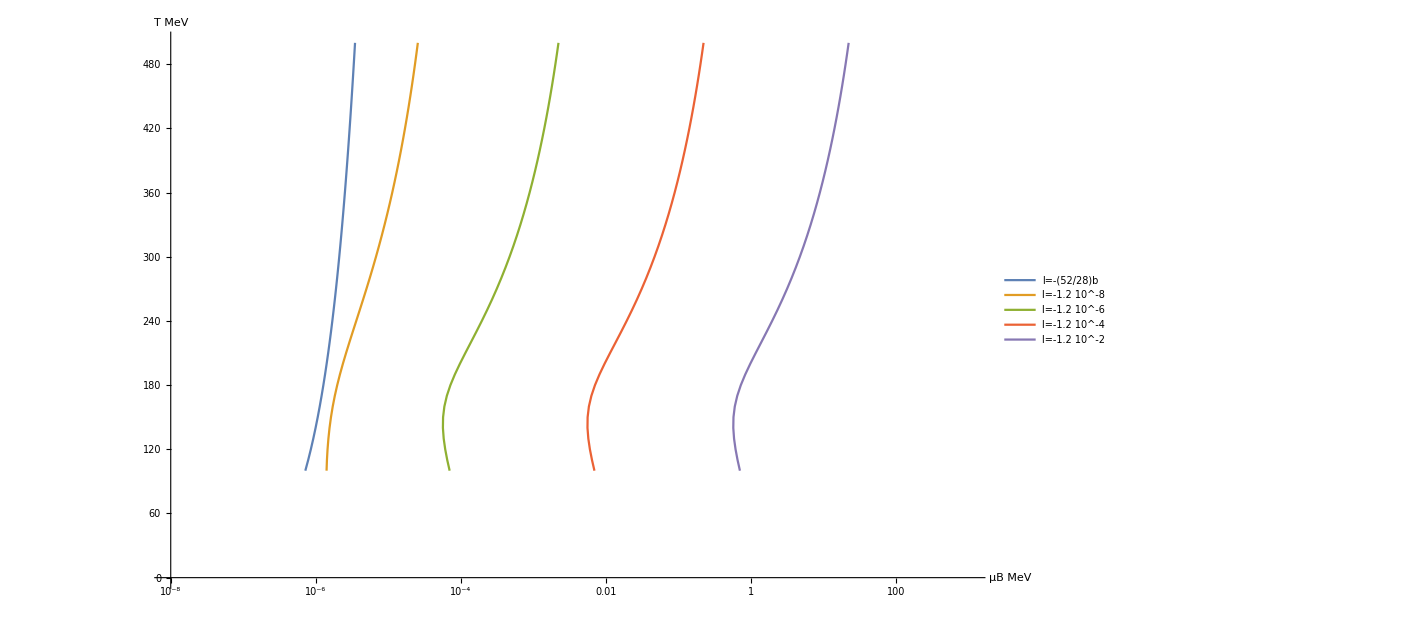

```mathematica
µql=.;
µql12m2=µexDF-µnuexDF;
µqTl12m2=Transpose[{µql12m2,TxDF}];

µLl12m2=.;
µLl12m2=-µnuexDF;
µLTl12m2=Transpose[{µLl12m2,TxDF}];


µbl12m2=.;
µbl12m2=µuxDF+2*(µuxDF+µexDF-µnuexDF);
µbTl12m2=Transpose[{µbl12m2,TxDF}];
```